Tensors are generalizations of vectors and matrices for arbitrary numbers of coordinate indices:
Scalars: 0
Vectors: 1
Matrices: 2
A tensor with n indices is a n-tensor. A tensor is invariant under multiplication by some matrix if multiplying every index by that matrix at the same time returns the same tensor. Likewise, a tensor is invariant under multiplication by a list of matrices if it is invariant under multiplication by each one.

Tensors with more than 2 indices show up in a variety of physical contexts, like 4 indices for the distortion of a solid object from pressure and shear.

```mathematica
NotebookEvaluate[NotebookDirectory[] <> "Rotation Reflection - Matrices Groups Polytopes.nb"]
```

### Reducing Tensors with Symmetries and Traces

End-cap vectors

That is my name for a vector for simplifying calculations on tensors. One takes the inner product of every tensor index with an end-cap vector:

A(i1,i2,...) * t1(i1) * t2(i2) * ...

thus giving a scalar function. One then does transforms on the tensors by doing those transforms on those end-cap vectors, or more precisely, those transforms’ transposes

If a tensor is symmetric over some indices, one can do further simplification by using  the same end cap for those indices.

Special invariant tensors

There are two kinds of tensors that are always invariant for rotations and reflections.

For the Kronecker delta or identity tensor del(i,j) for indices i, j, multiplication by matrix M gives transpose(M).M, and for rotation and reflection matrices, that is the identity matrix again.

The Levi-Civita tensor or antisymmetric symbol eps(i,j,...) is antisymmetric on all indices, with as many indices as dimensions, with in sorted order, eps(1,2, ...) = 1. Multiplying by matrix M gives eps times the determinant of M, giving +eps for rotations and -eps for reflections.

Decompositions of tensors by symmetry

A 2-tensor can be reduced to the sum of a symmetric part: A(j,i) = A(i,j) and an antisymmetric part: A(j,i) = - A(i,j). The antisymmetric part can be reduced further in 2 or 3 dimensions:

A(i,j) = A*eps(i,j) -- in 2 dimensions, to a scalar (pseudoscalar)
A(i,j) = A(k)*eps(i,j,k0 -- in 3 dimensions, to a vector (pseudovector or axial vector, as opposed to an ordinary vector, a polar vector)

Thus, a general tensor can be reduced to a sum of products of antisymmetric symbols and symmetric tensors. This is even true of tensors with more than two indices that have mixed symmetry.

Outer products of antisymmetric symbols are equal to sums of products of identity matrices:
eps(i,j,...)*eps(i’,j’,...) = sum over permutations P of (i’,j’...) of del(i,Pi’)*del(j,Pj’)*... * signature(P)
The signature is +1 for even permutations and -1 for odd ones, that being the count of interchanges necessary to make that permutation.
Thus
eps(i,j)*eps(i’,j’) = del(i,i’)*del(j,j’) - del(i,j’)*del(j,i’)
with (i’,j’) requiring no interchanges and (j’,i’) requiring one interchange.

For more than one antisymmetric symbol, one can use this identity for further reductions.

Decomposition of tensors by trace

The trace of a matrix M is the sum over its diagonal: sum over i of M(i,i). The trace can be generalized to more indices by summing over two of those indices.

A symmetric 2-tensor can be reduced to a scalar multiple of the identity tensor added to a symmetric traceless or trace-free (STF) 2-tensor. Likewise, a symmetric 3-tensor can be decomposed into a symmetric traceless one and a vector.

Thus, in 2 or 3 dimensions, one can reduce a general tensor to a combination of symmetric traceless tensors, identity matrices, and antisymmetric symbols.

End-cap vectors can be used to calculate traces. For indices with end caps t1 and t2 with components t1.1, t1.2, t2.1, ..., one calculates for end-capped tensor T d2T/d(t1.1)/d(t2.1) + d2T/d(t1.2)/d(t2.2) + ... for the same end cap, this is the Laplacian, and that can be used to calculate symmetric traceless tensors in end-capped form.

### Solutions

2D solutions

For two dimensions, the solutions are easy. For end-cap vector v = {v1,v2}, the end-capped tensor is f(v1+i*v2) + g(v1-i*v2). For an n-tensor, the two solutions are (v1+i*v2)^n and (v1-i*v2)^n. One can factor out the imaginary unit, i, with ((first)+(second))/2 and ((first)-(second))/(2i). For vmag = sqrt(v.v), these solutions are

vmag^n * ChebyshevT(n,v1/vmag) = vmag^n * cos(n*arctan(v2/v1))
vmag*(n-1) * v2 * ChebyshevU(n-1,v1/vmag) = vmag^n * sin(n*arctan(v2/v1))

For rotation, v1+i*v2 -> e^(i*a) * (v1+i*v2) ... v1-i*v2 -> e^(-i*a) * (v1-i*v2)
For reflection, v1+i*v2 -> e^(i*a) * (v1-i*v2) ... v1-i*v2 -> e^(-i*a) * (v1+i*v2)

For group C(n), both tensors with n*k indices are invariant.
For group D(n), only one of them is, though it may be a mixture of whatever forms that one uses to calculate them.

For continuous-limit groups SO(2) and O(2), no nontrivial ones.

3D solutions

Just as the 2D solutions can be expressed as trigonometric functions of the end-cap vector, the 3D solutions can be expressed as spherical harmonics of the end-cap vector. For vector v = {v1,v2,v3} with magnitude sqrt(v.v), the solutions are

vmag^n * SphericalHarmonicY(n,m,v/vmag

For overall index n and index m varying between -n and +n

For the axial groups with repeat factor nc, the possible values of m are k*nc for integer k.
C(nc) -- no further constraints
Ch(nc) ~ C(nc,h) -- (n - |m|) even
Cs(nc) ~ S(2*nc) -- nc even: (n - |k|) even -- nc odd: n even
Cv(nc) ~ C(nc,v) --  {m) + (-m) invariant (incl. m = 0)
D(nc) -- (n - |m}) even: (m) + (-m) invariant (incl. m = 0) -- (n - |m}) odd: (m) - (-m) invariant (no m = 0)
Dh(nc) ~ D(nc,h) -- (n - |m|) even: {m} + {-m} invariant (incl. m = 0)
Dd(nc) ~ D(nc,d) --  nc even: (n - |k|) even -- nc odd: n even -- all with {m} + {-m} invariant (incl. m = 0)

Continuous axial groups: m = 0
C(oo) -- no further constraints
Ch(oo) -- n even
Cv(oo) -- no further constraints
D(oo) -- n even
Dh(oo) -- n even

Quasi-spherical groups:
D2 -- invariants are:
even: combinations of squares of v1, v2, v3 -- l,m even, {m}+{-m} invariant
odd: v1*v2*v3 * (combination of those squares) -- l odd, m even, {m}-{m} invariant (no m=0)
Dh2 -- even only

Tetrahedral: the only two solutions:
l = 3, m = 2 odd: v1*v2*v3
l = 4, m = 0, m = 4 even: (v1^4+v2^4+v3^4) - 3(v1^2*v2^2+v1^2*v3^2+v2^2*v3^2)
Which groups have what:
T, Td: l = 3, 4
Th, O, Oh: l = 4
I, Ih: no nontrivial ones

For continuous-limit quasi-spherical groups SO(3) and O(3), no nontrivial ones.

## Transforms and End Caps

### Add and Remove End Cap

```mathematica
(* Args: tensor, endcap vector *)
```

```mathematica
AddEndCap[tens_,endcap_List] := Module[{nt},
nt = Length[Dimensions[tens]];
Nest[pt |-> Expand[pt.endcap],tens,nt]
]
```

```mathematica
(* Args: endcapped tensor, endcap, number of indices of target tensor *)
```

```mathematica
RemoveEndCap[ectens_,endcap_List,nt_?IsNonNegInt] := Nest[pt |-> ((v |-> D[pt,v]) /@ endcap),ectens,nt]/nt!
```

```mathematica
(* Args: endcapped tensor, endcap -- returns flattened list of tensor components *)
```

```mathematica
RemoveEndCapFlat[ectens_,endcap_List] := Fold[{pt, v} |-> Union[Flatten[Expand[CoefficientList[pt,v]]]],ectens,endcap]
```

```mathematica
(* End-cap trace: Laplacian: built-in function *)
```

### Transform a Tensor with a Set of Matrices

```mathematica
TensorMatMult[tens_,mat_List] :=  Module[{nt,ixsshift},
nt = Length[Dimensions[tens]];
ixsshift = RotateLeft[Range[nt]];
Nest[t |-> Transpose[Expand[t.mat],ixsshift],tens,nt]
]
```

```mathematica
TensorMListMult[tens_,mlist_List] :=  Table[TensorMatMult[tens,m],{m,mlist}]
```

```mathematica
TensorMatMultCheck[tens_,mat_List] :=  Expand[TensorMatMult[tens,mat] - tens]
```

```mathematica
TensorMListMultCheck[tens_,mlist_List] :=  Table[TensorMatMultCheck[tens,m],{m,mlist}]
```

```mathematica
(* Solution for a list of matrices, what we are interested in here. For a single matrix, use a list with only that one in it. *)
```

```mathematica
TensorMListMultSolve[tens_,mlist_List] := ToRules[Reduce[Thread[Flatten[TensorMListMultCheck[tens,mlist]]==0]]]
```

### Transform an Endcapped Tensor with a Set of Matrices

```mathematica
TensorECMatMult[ectens_,endcap_List,mat_List] := Expand[ectens /. Thread[endcap -> (mat.endcap)]]
```

```mathematica
TensorECMListMult[ectens_,endcap_List,mlist_List] := Table[TensorECMatMult[ectens,endcap,m],{m,mlist}]
```

```mathematica
TensorECMatMultCheck[ectens_,endcap_List,mat_List] := Expand[TensorECMatMult[ectens,endcap,mat] - ectens]
```

```mathematica
TensorECMListMultCheck[ectens_,endcap_List,mlist_List] := Table[TensorECMatMultCheck[ectens,endcap,m],{m,mlist}]
```

```mathematica
(* Solution for a list of matrices, what we are interested in here. For a single matrix, use a list with only that one in it. *)
```

```mathematica
TensorECMListMultSolve[ectens_,endcap_List,mlist_List] := ToRules[Reduce[Thread[RemoveEndCapFlat[TensorECMListMultCheck[ectens,endcap,mlist],endcap]==0]]]
```

### Find Invariant Combinations of a Linear Set of Tensors

```mathematica
TensorListMLSolve[tlist_List,mlist_List] := Module[{c,clist,clsol,clsd},
clist = Array[c,Length[tlist]];
clsol = clist /. TensorMListMultSolve[clist.tlist,mlist];
clsd = Table[D[clsol,cval],{cval,clist}];
clsd = Select[clsd,cl |-> Union[cl]=!={0}];
{clsd,If[Length[clsd] > 0,Expand[clsd.tlist],clsd]}
]
```

```mathematica
TensorECListMLSolve[ectlist_List,endcap_List,mlist_List] := Module[{c,clist,clsol,clsd},
clist = Array[c,Length[ectlist]];
clsol = clist /. TensorECMListMultSolve[clist.ectlist,endcap,mlist];
clsd = Table[D[clsol,cval],{cval,clist}];
clsd = Select[clsd,cl |-> Union[cl]=!={0}];
{clsd,If[Length[clsd] > 0,Expand[clsd.ectlist],clsd]}
]
```

```mathematica
(* The above functions threaded over lists of lists of tensors, working on each member list *)
```

```mathematica
TensorListListMLSolve[tlslist_List,mlist_List] := Table[TensorListMLSolve[tls,mlist],{tls,tlslist}]
```

```mathematica
TensorECListListMLSolve[ectlslist_List,endcap_List,mlist_List] := Table[TensorECListMLSolve[ectls,endcap,mlist],{ectls,ectlslist}]
```

## Solutions

```mathematica
(* Test the sequences of possible invariants for being traceless while endcapped *)
```

```mathematica
InvarSeqECTest[params___,endcap_List] := Map[iv |-> Laplacian[iv,endcap],InvarSeqEC[params,endcap],{2}]
```

### 2D Transforms - complex & even-odd

```mathematica
(* Rectangular coordinates x,y to complex coordinates (x+i*y), (x-i*y) *)
```

```mathematica
RectToCplx = {{1,I},{1,-I}};
```

```mathematica
RectToCplx.Matrix2DTrig[1,a].Inverse[RectToCplx] // TrigToExp // Expand
```

{{ⅇ^(ⅈ a),0},{0,ⅇ^(-ⅈ a)}}

```mathematica
(* Rotation changes the phases of the two vectors *)
```

```mathematica
RectToCplx.Matrix2DTrig[-1,a].Inverse[RectToCplx] // TrigToExp // Expand
```

{{0,ⅇ^(ⅈ a)},{ⅇ^(-ⅈ a),0}}

```mathematica
(* Reflection also flips the two vectors *)
```

### 2D Invariants

```mathematica
(* Easiest to calculate invariants with end caps *)
```

```mathematica
InvarEC["2D Cplx",n_?IsNonNegInt,endcap_List] := Table[({1,s*I}.endcap)^n,{s,{1,-1}}]
```

```mathematica
InvarEC["2D",n_?IsNonNegInt,endcap_List] := {{1,1}/2,{1,-1}/(2I)}.Expand[InvarEC["2D Cplx",n,endcap]] // Expand
```

```mathematica
(* Sequence calculated with end caps *)
```

```mathematica
InvarSeqEC["2D",nmax_?IsNonNegInt,endcap_List] := Module[{ecmat},
ecmat = {{endcap[[1]],-endcap[[2]]},{endcap[[2]],endcap[[1]]}};
NestList[v |-> Expand[ecmat.v],{1,0},nmax]
]
```

```mathematica
(* Sequence without end caps *)
```

```mathematica
InvarSeq["2D",nmax_?IsNonNegInt] := Module[{ec,t,ivec,ivs,iv},
ec = Array[t,2];
ivec = InvarSeqEC["2D",n,ec];
Table[ivs = ivec[[n+1]]; Table[RemoveEndCap[iv,ec,n],{iv,ivs}],{n,0,nmax}]
]
```

```mathematica
(* Solution for 2D groups: uses end caps *)
```

```mathematica
InvarSolve["2D",n_?IsNonNegInt,endcap_List,params__] := TensorECListListMLSolve[InvarSeqEC["2D",n,endcap],endcap,Group2D[params]]
```

### 3D Invariants

```mathematica
(* Associated Legendre polynomals without the(1-x^2)^(m/2) part, multiplied by mag^((n-m)/2) and with arg x = axl/sqrt(mag) These are intended for end-cap duty. *)
```

```mathematica
AssocLgdrPolySeq[nmax_?IsNonNegInt,m_?IsNonNegInt,mag_,axl_] := Module[{polys={},next},
If[nmax < m,Return[polys]];
AppendTo[polys,(-1)^m*(2m-1)!!];
If[nmax == m,Return[polys]];
AppendTo[polys,First[polys]*(2m+1)*axl];
If[nmax == m+1,Return[polys]];
Do[next = Expand[1/(n-m)*((2n-1)*axl*polys[[-1]] - (n+m-1)*mag*polys[[-2]])]; AppendTo[polys,next],{n,m+2,nmax}];
Return[polys];
]
```

```mathematica
(* Should return zeros *)
```

```mathematica
AssocLgdrPolySeqTest[nmax_?IsNonNegInt,m_?IsNonNegInt,x_] := (1-x^2)^(m/2)AssocLgdrPolySeq[nmax,m,1,x] - Table[LegendreP[n,m,x],{n,m,nmax}] // Expand
```

```mathematica
AssocLgdrPolySeqTest[nmax_?IsNonNegInt,x_] := Table[AssocLgdrPolySeqTest[nmax,m,x],{m,0,nmax}]
```

```mathematica
InvarSeqEC["3D",nmax_?IsNonNegInt,endcap_List] := Module[{ecmag,ecaxl,lgsqs,cssqs},
ecaxl = {0,0,1}.endcap;
ecmag = endcap.endcap;
lgsqs = Table[AssocLgdrPolySeq[n,m,ecmag,ecaxl],{m,0,nmax}];
cssqs = InvarSeqEC["2D",n,Take[endcap,2]];
Table[Flatten[Table[Expand[If[m>0,cssqs[[m+1]],{1}]*lgsqs[[m+1,n-m+1]]],{m,0,n}],1],{n,0,nmax}]
]
```

```mathematica
InvarSolve["3D",nmax_?IsNonNegInt,endcap_List,params___] := TensorECListListMLSolve[InvarSeqEC["3D",nmax,endcap],endcap,Group3D[params]]
```

```mathematica
(* ncyc is the multiple of m that is accepted: the axial-group size parameter *)
```

```mathematica
InvarSeqEC["3D Axial",nmax_?IsNonNegInt,ncyc_?IsNonNegInt,endcap_List] := Module[{ecmag,ecaxl,lgsqs,cssqs},
ecaxl = {0,0,1}.endcap;
ecmag = endcap.endcap;
lgsqs = Table[AssocLgdrPolySeq[nmax,m,ecmag,ecaxl],{m,0,nmax,ncyc}];
cssqs = InvarSeqEC["2D",nmax,Take[endcap,2]];
Table[Flatten[Table[Expand[If[m>0,cssqs[[m+1]],{1}]*lgsqs[[m/ncyc+1,n-m+1]]],{m,0,n,ncyc}],1],{n,0,nmax}]
]
```

```mathematica
InvarSolve["3D Axial",nmax_?IsNonNegInt,endcap_List,type_,ncyc_?IsPosInt] := TensorECListListMLSolve[InvarSeqEC["3D Axial",nmax,ncyc,endcap],endcap,Group3D[type,ncyc]]
```

```mathematica
(* Tetrahedral even *)
```

```mathematica
InvarSeqEC["3D TetEven",nmax_?IsPosInt,endcap_List] := Module[{ecmag,ecaxl,lgsqs,cssqs},
ecaxl = {0,0,1}.endcap;
ecmag = endcap.endcap;
lgsqs = Table[AssocLgdrPolySeq[n,m,ecmag,ecaxl],{m,0,nmax,4}];
cssqs = InvarSeqEC["2D",n,Take[endcap,2]];
Table[Flatten[Table[Expand[cssqs[[m+1,1]]*lgsqs[[m/4+1,n-m+1]]],{m,0,n,4}],1],{n,0,nmax,4}]
]
```

```mathematica
InvarSolve["3D TetEven",nmax_?IsNonNegInt,endcap_List,type_] := TensorECListListMLSolve[InvarSeqEC["3D TetEven",nmax,endcap],endcap,Group3D[type]]
```

```mathematica
(* Tetrahedral odd *)
```

```mathematica
InvarSeqEC["3D TetOdd",nmax_?IsPosInt,endcap_List] := Module[{ecmag,ecaxl,lgsqs,cssqs},
ecaxl = {0,0,1}.endcap;
ecmag = endcap.endcap;
lgsqs = Table[AssocLgdrPolySeq[n,m,ecmag,ecaxl],{m,2,nmax,4}];
cssqs = InvarSeqEC["2D",n,Take[endcap,2]];
Table[Flatten[Table[Expand[cssqs[[m+1,2]]*lgsqs[[(m-2)/4+1,n-m+1]]],{m,2,n,4}],1],{n,3,nmax,4}]
]
```

```mathematica
InvarSolve["3D TetOdd",nmax_?IsNonNegInt,endcap_List,type_] := TensorECListListMLSolve[InvarSeqEC["3D TetOdd",nmax,endcap],endcap,Group3D[type]]
```

```mathematica
(* Both the even solution and the odd solution *)
```

```mathematica
TetrahedralKnown[endcap_List] := Module[{t1,t2,t3},
{t1,t2,t3} = endcap;
{(t1^4+t2^4+t3^4)-3*(t1^2*t2^2+t1^2*t3^2+t2^2*t3^2),t1*t2*t3}
]
```

```mathematica
TetrahedralKnownTest[endcap_List] := (tn |-> {Laplacian[tn,endcap], tn - ((sq |-> {{1,0,0,0,0,0,0,1/168,0}.sq[[5]],{0,0,0,0,1/30,0,0}.sq[[4]]}) @ InvarSeqEC["3D",4,endcap])}) @ TetrahedralKnown[endcap] // Expand
```

### Cubic symmetry

There are only two nontrivial known solutions for cubic symmetry: the l = 3 odd one and the l = 4 even one.

Can those be shown to be the only ones?

Even solutions: Y(4n,4k) + Y(4n,-4k) where k is 0 to n
Odd solutions: Y(4n-1,4k+2) - Y(4n-1,-(4k+2)) where k is 0 to n-1

For end-cap vector {t1,t2,t3}, the even solutions have t1^(4n) + t2^(4n) + t3^(4n) + ...  and the odd solutions t1^(4n-3)*t2*t3 + t2^(4n-3)*t1*t3 + t3^(4n-3)*t1*t2 + ...

Expand these solutions around t3 >> t1, t2 and t1 >> t2, t3

Even:
Expand Y(4n,0) around t3 >> t1,t2 and t1 >> t2,t3
Expand Y(4n,4n) even around t1 >> t2,t3

Odd:
Expand Y(4n-1,2) around t3 >> t1,t2 and t1 >> t2,t3
Expand(Y(4n-1,4n-2) odd around t1 >> t2,t3

We need only these ones, because they are not canceled by intermediate terms Y(4n,4k) and Y(4n-1,4k+2).

Conclusion: these two solutions are the only ones.

```mathematica
(* Whether even or odd, which member for each n, which t^n component, which next component, step through array, offset *)
```

```mathematica
SerExp["Even",1,{3,1},{0,1},n_] := {1,-n(n-1)/4}
```

```mathematica
SerExp["Even",1,{1,2,3},{0,2},n_] := (-1)^n*(2n-1)!!/(2n)!!*{1,n,-2n^2}
```

```mathematica
SerExp["Even",-2,{1,2},{1,1},n_] := (-1)^(n+1)*(2n+1)!!*{1,-n(n+1)/2}
```

```mathematica
SerExp["Odd",5,{3,1},{2,1},n_] := (n+1)(n+2)(n+3)(n+4)/4*{1,-n(n-1)/12}
```

```mathematica
SerExp["Odd",5,{1,2,3},{3,2},n_] := 2*(-1)^n*(2n+5)!!/(2n)!!*{1,n,-2n(n+2)/3}
```

```mathematica
SerExp["Odd",-3,{1,2},{2,1},n_] := (-1)^(n+1)*(n+1)*(2n+3)!!*{1,-n(n-1)/6}
```

```mathematica
SerExpTest[nmax_?IsNonNegInt,endcap_List] := Module[{t1,t2,t3,ivslst,iv,ivc,df1,df2,df3,df4,df5,df6},
{t1,t2,t3} = endcap;
ivslst = InvarSeqEC["3D",nmax,endcap];
df1 = Table[iv = ivslst[[n+1,1]];ivc = Coefficient[iv,t3,n-2]; {Coefficient[iv,t3,n],Coefficient[ivc,t1,2]}-SerExp["Even",1,{3,1},{0,1},n],{n,0,nmax}];
df2 = Table[iv = ivslst[[n+1,1]];ivc = Coefficient[iv,t1,n-2]; {Coefficient[iv,t1,n],Coefficient[ivc,t2,2],Coefficient[ivc,t3,2]}-SerExp["Even",1,{1,2,3},{0,2},n/2],{n,0,nmax,2}];
df3 = Table[iv = ivslst[[n+1,-2]];ivc = Coefficient[iv,t1,n-2]; {Coefficient[iv,t1,n],Coefficient[ivc,t2,2]}-SerExp["Even",-2,{1,2},{1,1},n-1],{n,1,nmax}];
df4 = Table[iv = Expand[ivslst[[n+1,5]]/(t1*t2)];
ivc = Coefficient[iv,t3,n-4]; {Coefficient[iv,t3,n-2],Coefficient[ivc,t1,2]}-SerExp["Odd",5,{3,1},{2,1},n-2],{n,2,nmax}];
df5 = Table[iv = Expand[ivslst[[n+1,5]]/(t1*t2*t3)];ivc = Coefficient[iv,t1,n-5]; {Coefficient[iv,t1,n-3],Coefficient[ivc,t2,2],Coefficient[ivc,t3,2]}-SerExp["Odd",5,{1,2,3},{3,2},(n-3)/2],{n,3,nmax,2}];
df6 = Table[iv = Expand[ivslst[[n+1,-3]]/(t2*t3)];ivc = Coefficient[iv,t1,n-4]; {Coefficient[iv,t1,n-2],Coefficient[ivc,t2,2]}-SerExp["Odd",-3,{1,2},{2,1},n-2],{n,2,nmax}];
{df1,df2,df3,df4,df5,df6}
]
```

```mathematica
(* n starts at 1 for both the even and the odd one *)
```

```mathematica
SECmbn["Even",n_] := Module[{se1,se2,se3},
se1 = SerExp["Even",1,{3,1},{0,1},4n];
se2 = SerExp["Even",1,{1,2,3},{0,2},2n];
se3 = SerExp["Even",-2,{1,2},{1,1},4n-1];
{se1[[2]],se2[[3]],se2[[2]]+(se1[[1]]-se2[[1]])*se3[[2]]/se3[[1]]}
]
```

```mathematica
SECmbn["Odd",n_] := Module[{se1,se2,se3},
se1 = SerExp["Odd",5,{3,1},{2,1},4n-3];
se2 = SerExp["Odd",5,{1,2,3},{3,2},2n-2];
se3 = SerExp["Odd",-3,{1,2},{2,1},4n-4];
{se1[[2]],se2[[3]],se2[[2]]+(se1[[1]]-se2[[1]])*se3[[2]]/se3[[1]]}
]
```

```mathematica
SECmbn["Even",1]
```

{-3,-3,-3}

```mathematica
SECmbn["Odd",1]
```

{0,0,0}

```mathematica
SECmbnTbl[type_,nmax_] := Table[SECmbn[type,n],{n,Switch[type,"Even",1,"Odd",2],nmax}]
```

```mathematica
SECmbnTblNorm[type_,nmax_] := #/N[Total[#]]& /@ SECmbnTbl[type,nmax]
```

```mathematica
SECmbnPlot[type_,nmax_] := ListPlot[Transpose[SECmbnTblNorm[type,nmax]],Joined->True]
```

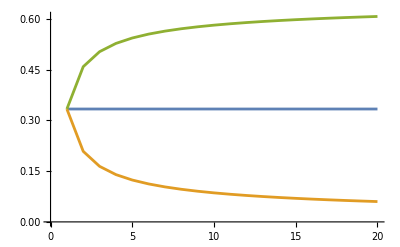

```mathematica
SECmbnPlot["Even",20]
```

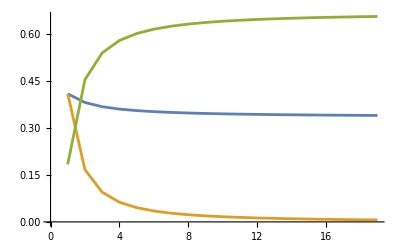

```mathematica
SECmbnPlot["Odd",20]
```

## Applications

### Materials Properties

These kinds of tensors are very useful in materials-properties applications, where they can quantify anisotropy, variation by direction, in convenient ways.

Elasticity

Materials change their size and shape in response to applied pressure and stress, and in the linear limit, the strain tensor, as it’s called, is a linear function of the stress tensor, as it’s called.

The stress tensor P(i,j) is the pressures and shears in tensor form. It is symmetric.

The strain tensor is the amount of distortion, the change of offset by position. For offset X(i) and derivative by position D(i,...), E(i,j) = (1/2)*(D(i,X(j)) + D(j,X(i)). It also is symmetric.

P(i,j) = (1/2)*K(i,j,k,l)*E(k,l)

K has several symmetries: i<->j, k<->l, and (i,j)<->(k,l).

Its STF decomposition is 2 scalars, 2 2-tensors, and 1 4-tensor: K0L, K0T, K2L, K2T, K4

K(i,j,k,l) = K0L*d(i,j)*d(k,l) + K0T*(d(i,k)*d(j,l) + d(i,l)*d(j,k))
+ (K2L(i,j)*d(k,l) + K2L(k,l)*d(i,j)) + (K2T(i,k)*d(j,l) + K2T(i,l)*d(j,k) + K2T(j,k)*d(i,l) + K2T(j,l)*d(i,k))
+ K4(i,j,k,l)

Fluid: K0L
Isotropic solid: K0L, K0T
Cubic lattice: K0L, K0T, (with all lattice directions) K4
Hexagonal lattice: K0L, K0T, (with normal-to-hexagonal direction) K2L, K2T, K4

Elasticity tensor - Wikipedia
https://en.wikipedia.org/wiki/Elasticity_tensor
Elasticity/Constitutive relations - Wikiversity
https://en.wikiversity.org/wiki/Elasticity/Constitutive_relations

This part of the hexagonal-lattice solution is also that part of the general solution for one direction of anisotropy. For direction vector w with wmag = w.w, these tensors are:
T2(i,j) = w(i)*w(j) - (1/3)*wmag*d(i,j)
T3(i,j,k) = w(i)*w(j)*w(k) - (1/5)*wmag*(w(i)*d(j,k) + index interchanges)
T4(i,j,k,l) = w(i)*w(j)*w(k)*w(l) - (1/7)*wmag*(w(i)*w(j)*d(k,l) + ii’s) + (1/35)*wmag^2*(d(i,j)*d(k,l)+ii’s)

One can get the cubic tensor by summing T4 over each axis.

Electric permittivity

(Polarization) = (dielectric tensor) . (electric field)
Dielectric tensor K: its STF decomposition is 1 scalar, 1 vector, and 1 2-tensor:
K(i,j) = (symmetric) K0*d(i,j) + K2(i,j) + (antisymmetric)  e(i,j,k)*K1(k)

K1: from applied magnetism.

Permittivity - Wikipedia
https://en.wikipedia.org/wiki/Permittivity

Anisotropy has the consequence of making different polarizations of light be refracted by different amounts,
Birefringence - Wikipedia
https://en.wikipedia.org/wiki/Birefringence

Magnetic susceptibility

(Magnetization) = (magnetic-susceptibility tensor) . (magnetic field)
Like the symmetric part of electric permittivity.

Magnetic susceptibility - Wikipedia
https://en.wikipedia.org/wiki/Magnetic_susceptibility

Electrostriction and magnetostriction

(Strain tensor) = K . (polarization) . (polarization)
K: elasticity-like tensor

Electrostriction - Wikipedia
https://en.wikipedia.org/wiki/Electrostriction
Magnetostriction - Wikipedia
https://en.wikipedia.org/wiki/Magnetostriction

Piezoelectricity and piezomagnetism

(Polarization) = K . (strain tensor)
K: 3-index tensor, with STF decomposition 2 K1, 1 K3.

Piezoelectricity - Wikipedia
https://en.wikipedia.org/wiki/Piezoelectricity
Piezomagnetism - Wikipedia
https://en.wikipedia.org/wiki/Piezomagnetism

### Crystallographic Groups

These are point groups constrained to be symmetries of points in a crystal lattice.
Crystallographic point group - Wikipedia
https://en.wikipedia.org/wiki/Crystallographic_point_group

These tables go up to 4 tensor dimensions

Two Dimensions
Number of Groups: 10
C, D: 1, 2, 3, 4, 6

Tensor dimensions:
1: 0, 1, 2, 3, 4 (all)
2: 0, 2, 4
3: 0, 3
4: 0, 4
6: 0
Nonzero numbers of dimensions have 2 tensors for C(n) and 1 tensor for D(n)

Three Dimensions
Number of groups: 32
(modified Schoenflies notation)
C, Ch, Cv, D, Dh : 1, 2, 3, 4, 6
Cs, Dd: 1, 2, 3
T, Th, Td, O, Oh
Isomorphisms: Ch1 ~ Cv1, C2 ~ D1, Ch2 ~ Dd1, Cv2 ~ Dh1
Alternate notations: Ci ~ Cs1, Cs ~ Ch1, V ~ D2, Vh ~ Dh2, Vd ~ Dd2, C3i ~ Cs3

Tensor dimension, second quantum number
C1: 0: (0), 1: (0, 2 of 1), 2: (0, 2 of 1, 2 of 2), 3: (0, 2 of 1, 2 of 2, 2 of 3), 4: (0, 2 of 1, 2 of 2, 2 of 3, 2 of 4) (all)
C2: 0: (0), 1: (0), 2: (0, 2 of 2), 3: (0), 4: (0, 2 of 2, 2 of 4)
C3: 0, (0), 1: (0), 2: (0), 3: (0, 2 of 3), 4: (0, 2 of 3)
C4: 0: (0), 1: (0), 2: (0), 3: (0), 4: (0, 2 of 4)
C6: 0: (0), 1: (0), 2: (0), 3: (0), 4: (0)
Ch1: 0: (0), 1: (2 of 1), 2: (0, 2 of 2), 3: (2 of 1, 2 of 3), 4: (0,  2 of 2, 2 of 4)
Ch2: 0: (0), 1: (), 2: (0, 2 of 2), 3: (), 4: (0,  2 of 2, 2 of 4)
Ch3: 0: (0), 1: (), 2: (0), 3: ( 2 of 3), 4: (0)
Ch4: 0: (0), 1: (), 2: (0), 3: (), 4: (0, 2 of 4)
Ch6: 0: (0), 1: (), 2: (0), 3: (), 4: (0)
Cs1: 0: (0), 1: (), 2: (0, 2 of 1, 2 of 2), 3: (), 4: (0, 2 of 1, 2 of 2, 2 of 3, 2 of 4) 
Cs2: 0: (0), 1: (), 2: (0), 3: (2 of 2), 4: (0, 2 of 4)
Cs3: 0: (0), 1: (), 2: (0), 3: (), 4: (0, 2 of 3) 
Cv1: 0: (0), 1: (0, 1 of 1), 2: (0, 1 of 1, 1 of 2), 3: (0, 1 of 1, 1 of 2, 1 of 3), 4: (0, 1 of 1, 1 of 2, 1 of 3, 1 of 4)
Cv2: 0: (0), 1: (0), 2: (0, 1 of 2), 3: (0,  1 of 2), 4: (0, 1 of 2, 1 of 4)
Cv3: 0: (0), 1: (0), 2: (0), 3: (0, 1 of 3), 4: (0, 1 of 3)
Cv4: 0: (0), 1: (0), 2: (0), 3: (0), 4: (0, 1 of 4)
Cv6: 0: (0), 1: (0), 2: (0), 3: (0), 4: (0)
D1: 0: (0), 1: (1 of 1), 2: (0, 1 of 1, 1 of 2), 3: (1 of 1, 1 of 2, 1 of 3), 4: (0, 1 of 1, 1 of 2, 1 of 3, 1 of 4)
D2: 0: (0), 1: (), 2: (0, 1 of 2), 3: (1 of 1, 1 of 3), 4: (0, 1 of 2, 1 of 4)
D3: 0: (0), 1: (), 2: (0), 3: (1 of 3), 4: (0, 1 of 3)
D4: 0: (0), 1: (), 2: (0), 3: (), 4: (0, 1 of 4)
D6: 0: (0), 1: (), 2: (0), 3: (), 4: (0)
Dh1: 0: (0), 1: (1 of 1), 2: (0, 1 of 2), 3: (1 of 1,1 of 3), 4: (0, 1 of 2, 1 of 4)
Dh2: 0: (0), 1: (), 2: (0, 1 of 2), 3: (), 4: (0, 1 of 2, 1 of 4)
Dh3: 0: (0), 1: (), 2: (0), 3: (1 of 3), 4: (0)
Dh4: 0: (0), 1: (), 2: (0), 3: (), 4: (0, 1 of 4)
Dh6: 0: (0), 1: (), 2: (0), 3: (), 4: (0)
Dd1: 0: (0), 1: (), 2: (0, 1 of 1, 1 of 2), 3: (), 4: (0, 1 of 1, 1 of 2, 1 of 3, 1 of 4)
Dd2: 0: (0), 1: (), 2: (0), 3: (1 of 2), 4: (0, 1 of 4)
Dd3: 0: (0), 1: (), 2: (0), 3: (), 4: (0, 1 of 3)
T, Td: 0: (0), 1: (), 2: (), 3: (1 of 3), 4: (0 mixed with 1 of 4)
Th, O, Oh: 0: (0), 1: (), 2: (), 3: (), 4: (0 mixed with 1 of 4)